# Quantum Mechanics

## Perturbation Theory

## Time-Independent Perturbation

### A Toy Model of Qubit

#### General Ideas of Perturbation Theory

Perturbation theory: a set of approximation schemes that allows us to extend our knowledge about an exactly solvable quantum system to its vicinity (in the parameter space).

Why do we need perturbation theory?

Exact solutions are rare. ⇒ We have to rely on perturbation theory to go beyond them and make the most of these exact solutions.

Separation of scales: physics often takes place at different energy scales, e.g. … → quarks (GeV) → nucleus (MeV) → atoms (eV) → molecules (100meV) → … ⇒ We can refine our descriptions by adding perturbative corrections progressively.

What are the central problems in perturbation theory?

Time-independent perturbation: given the spectrum (eigenstates and eigenenergies) of H_0, find the spectrum of H=H_0+λ V, in power series of λ (given that λ is small).

Time-dependent perturbation: given the (bare) propagator U_0(t)=e^(-ⅈ H_0 t), find the propagator

U(t)=𝒯 exp(-ⅈ ∫_0^t ⅆ t' H(t')),
H(t)=H_0+λ V(t),

in power series of λ (given that λ is small). [We will explain the notations in Eq. (DisplayFormulaNumbered) later.]

How is perturbation theory useful?

Conceptually: to establish effective Hamiltonians, to analyze renormalization group flows …

Practically: to calculate scattering amplitudes, response functions, spectral weights …

#### Qubit Model and its Exact Solution

Let us start with a toy model of a single qubit. Consider

H(λ)=H_0+λ V,

where H_0=σ^z and V=σ^x, s.t. H(λ) can be more explicitly written as

H(λ)=σ^z+λ σ^x
≏(1 | λ
λ | -1).

What are the eigenenergies and eigenstates of H(λ)?

H(λ)ψ_±(λ)=E_±(λ)ψ_±(λ).

Eigenenergies

E_±(λ)=±√(1+λ^2).

Eigenstates

ψ_+(λ)=((1+√(1+λ^2))↑+λ↓)/(√(2(1+λ^2+√(1+λ^2)))),
ψ_-(λ)=((1+√(1+λ^2))↓-λ↑)/(√(2(1+λ^2+√(1+λ^2)))).

#### Taylor Expansion

Assuming λ is small (i.e. λ≪1), Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) can be expanded in power series of λ

As a reminder, the Taylor expansion of a function f(λ) is given by

f(λ)=∑_(k=0)^∞ (∂_λ^k f(0))/(k!)λ^k
=f(0)+f'(0)λ+(f''(0))/2 λ^2+(f^(3)(0))/6 λ^3+….

Applying Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we get

E_±=±(1+λ^2/2-λ^4/8+…),

ψ_+(λ)=↑+λ/2↓-λ^2/8↑-(3 λ^3)/16↓+(11 λ^4)/128↑+…,
ψ_-(λ)=↓-λ/2↑-λ^2/8↓+(3 λ^3)/16↑+(11 λ^4)/128↓+….

Goal: obtain these power series without first calculating the exact solution! - This is possible as long as we know how to evaluate the derivatives ∂_λ^n E(0) and ∂_λ^n ψ_±(0).

The perturbation theory is essentially an iterative algorithm to calculate these derivatives order by order, based on our knowledge about H_0 and V.

### Non-Degenerate Perturbation Theory

#### Problem Setup

The starting point is the following Hamiltonian (linearly parameterized by λ)

H(λ)=H_0+λ V.

This implies

H(0)=H_0,
∂_λ H(0)=V,
∂_λ^2 H(0)=∂_λ^3 H(0)=…=0.

To simplify the notation, we will suppress the argument λ if it is evaluated at λ=0.

H=H_0,
∂_λ H=V,
∂_λ^2 H=∂_λ^3 H=…=0.

Rule: Everything is treated as a function of λ, like f(λ). But if the dependence on λ is not explicitly spelt out, we assume it to be the function evaluated at λ=0, i.e. f≡f|_(λ=0)=f(0).

Consider the eigen equation

H(λ)n(λ)=E_n(λ)n(λ).

For each given λ, there is a different H(λ), and hence a different set of E_n(λ) and n(λ), labeled by n=1,2,3,….

E_n(λ) is the nth energy level. It is a real number depending on λ.

n(λ) is the nth eigenstate (in correspondence to E_n(λ)). It is a state vector in the Hilbert space that can change with λ. Note: The notation n(λ) does not imply that the index n is λ dependent, it should be understood as

n(λ)=∑_m ψ_nm(λ)m.

We assume a discrete spectrum without degeneracy, such that the “nth” level/state is uniquely defined. [The case with degeneracy will be discussed latter.]

Statement of the problem: suppose we know the eigenenergies and eigenstates at and only at λ=0,

Hn=E_n n,

and we also know what the perturbation is: V=∂_λ H,

V_mn=mVn=m∂_λ Hn,

calculate E_n(λ) and n(λ) in power series of λ (to any desired order) in terms of E_n, V_mn and n.

#### Hellmann-Feynman Theorems

Applying ∂_λ  to both sides of Hn=E_n n,

∂_λ Hn+H∂_λ n=∂_λ E_nn+E_n∂_λ n.

Note: ∂_λ n stands for the derivative of the state n (not the index n)

∂_λ n=(∑_m ∂_λ ψ_nm(λ)m)_(λ=0).

It does not imply that the integer index n can be differentiated.

Overlap with m from the left,

m∂_λ Hn+mH∂_λ n=∂_λ E_nmn+E_n m∂_λ n.

Using mH=m E_m,

m∂_λ Hn+E_m m∂_λ n=∂_λ E_nmn+E_n m∂_λ n
⇒m∂_λ Hn=∂_λ E_nmn+(E_n-E_m)m∂_λ n.

Note that ∂_λ H=V and mn=δ_mn,

V_mn=mVn=∂_λ E_n δ_mn+(E_n-E_m)m∂_λ n.

This establishes a relation between the matrix element V_mn (of the perturbation) and the derivatives ∂_λ E_n and ∂_λ n.

When m=n, Eq. (DisplayFormulaNumbered) implies

∂_λ E_n=V_nn.

This is the first Hellmann-Feynman theorem.

When m≠n, Eq. (DisplayFormulaNumbered) implies

m∂_λ n=V_mn/(E_n-E_m),
∂_λ mn=V_mn/(E_m-E_n).

This is the second Hellmann-Feynman theorem. Tip: the energy denominator is always given by the energy of the state that is being differentiated minus the energy of the other state.

The Hellmann-Feynman theorems tell us how the derivative of the energy ∂_λ E_n or the state ∂_λ n and ∂_λ m on the left-hand-side is related to something on the right-hand-side which does not contain ∂_λ . ⇒ This effectively reduces the order of ∂_λ  by one. ⇒ Applying them iteratively, we will be able to calculate the derivatives to any order for both energies and states, which are all we need to construct the power series of the perturbative expansion.

#### Energy Corrections

According to the Taylor expansion,

E_n(λ)=∑_(k=0)^∞ (∂_λ^k E_n)/(k!)λ^k=E_n+∂_λ E_nλ+1/2∂_λ^2 E_n λ^2+….

We already know from Eq. (DisplayFormulaNumbered) that

∂_λ E_n=V_nn=n∂_λ Hn.

We continue to evaluate

∂_λ^2 E_n=∂_λ n∂_λ Hn
=∂_λ n∂_λ Hn+n∂_λ^2 Hn+n∂_λ H∂_λ n.

Note that ∂_λ^2 H=0 according to the setup in Eq. (DisplayFormulaNumbered).

∂_λ^2 E_n=∂_λ n∂_λ Hn+n∂_λ H∂_λ n
=∑_m (∂_λ nmm∂_λ Hn+n∂_λ Hmm∂_λ n)
=∑_m (V_nm/(E_n-E_m)V_mn+V_nm V_mn/(E_n-E_m))
=2∑_m (V_nm V_mn)/(E_n-E_m).

But, wait a moment … The energy denominator diverges when m=n, what is wrong? - Note that Eq. (DisplayFormulaNumbered) only holds for m≠n, so we must be careful. Let us restart from the 2nd line of Eq. (DisplayFormulaNumbered),

∂_λ^2 E_n=∑_m (∂_λ nmm∂_λ Hn+n∂_λ Hmm∂_λ n)
=∑_(m≠n) (∂_λ nmm∂_λ Hn+n∂_λ Hmm∂_λ n)+(∂_λ nnn∂_λ Hn+n∂_λ Hnn∂_λ n)
=2∑_(m≠n) (V_nm V_mn)/(E_n-E_m)+V_nn(∂_λ nn+n∂_λ n)
=2∑_(m≠n) (V_nm V_mn)/(E_n-E_m)+V_nn∂_λ nn.

Given that nn=1, taking ∂_λ  on both sides, ∂_λ nn=∂_λ 1=0. So

∂_λ^2 E_n=2∑_(m≠n) (V_nm V_mn)/(E_n-E_m).

So to the 2nd order in λ, the perturbative correction to the energy is given by

E_n(λ)=E_n+V_nn λ+∑_(m≠n) (V_nm V_mn)/(E_n-E_m)λ^2+….

##### Comment on Gauge Fixing

In fact, n∂_λ n is the connection of the vector bundle which can always be set to zero by gauge fixing along the path of λ. To see this, we start with

nn=1
⇒∂_λ nn+n∂_λ n=∂_λ nn=∂_λ 1=0
⇒Ren∂_λ n=0.

So n∂_λ n can only be purely imaginary. But we are free to perform the gauge transformation

n(λ)→e^(ⅈ ϕ(λ))n(λ),

under which,

n∂_λ n→n∂_λ n+ⅈ ∂_λ ϕ.

We can always choose ∂_λ ϕ to transform n∂_λ n to zero. So in addition to Eq. (DisplayFormulaNumbered), we can further require

n∂_λ n=∂_λ nn=0.

#### State Corrections

According to the Taylor expansion,

n(λ)=∑_(k=0)^∞ (∂_λ^k n)/(k!)λ^k=n+∂_λ nλ+1/2∂_λ^2 n λ^2+….

By Eq. (DisplayFormulaNumbered), we know

∂_λ n=∑_(m≠n) mm∂_λ n=∑_(m≠n) mV_mn/(E_n-E_m).

Let us continue to calculate the next order derivative [Please bear with me ...]

∂_λ^2 n=∂_λ ∑_(m≠n) m(m∂_λ Hn)/(E_n-E_m)
=∑_(m≠n) (∂_λ m(m∂_λ Hn)/(E_n-E_m)+m(∂_λ m∂_λ Hn)/(E_n-E_m)+m(m∂_λ H∂_λ n)/(E_n-E_m)-m(m∂_λ Hn)/(E_n-E_m)^2(∂_λ E_n-∂_λ E_m))
=∑_(m≠n) (∑_(l≠m) l V_lm/(E_m-E_l)V_mn/(E_n-E_m)+∑_(l≠m) m V_ml/(E_m-E_l)V_ln/(E_n-E_m)+∑_(l≠n) m V_ml/(E_n-E_m)V_ln/(E_n-E_l)-m V_mn/(E_n-E_m)^2(V_nn-V_mm))

Push l=m or l=n terms out of the summation, so as to combine the first three summations under ∑_(l≠m,n)  (sum over l excluding both m and n),

∂_λ^2 n=∑_(m≠n) (∑_(l≠m,n) (l V_lm/(E_m-E_l)V_mn/(E_n-E_m)+m V_ml/(E_m-E_l)V_ln/(E_n-E_m)+m V_ml/(E_n-E_m)V_ln/(E_n-E_l))+n V_nm/(E_m-E_n)V_mn/(E_n-E_m)+m V_mn/(E_m-E_n)V_nn/(E_n-E_m)+m V_mm/(E_n-E_m)V_mn/(E_n-E_m)-m(V_mn V_nn)/(E_n-E_m)^2+m(V_mn V_mm)/(E_n-E_m)^2)
=∑_(m≠n) (∑_(l≠m,n) (l V_lm/(E_m-E_l)V_mn/(E_n-E_m)+m V_ml/(E_m-E_l)V_ln/(E_n-E_m)+m V_ml/(E_n-E_m)V_ln/(E_n-E_l))-n(V_nm V_mn)/(E_n-E_m)^2-2m(V_mn V_nn)/(E_n-E_m)^2+2m(V_mn V_mm)/(E_n-E_m)^2)

The double summation ∑_(m≠n) ∑_(l≠m,n) means to sum over l and m, under the constraint that l,m,n are mutually exclusive. The summation is symmetric under the exchange of l and m. So for the first term in Eq. (DisplayFormulaNumbered),

∑_(m≠n) ∑_(l≠m,n) l V_lm/(E_m-E_l)V_mn/(E_n-E_m)=∑_(m≠n) ∑_(l≠m,n) m V_ml/(E_l-E_m)V_ln/(E_n-E_l),

therefore

∂_λ^2 n=∑_(m≠n) (∑_(l≠m,n) m V_ml V_ln(1/((E_l-E_m)(E_n-E_l))+1/((E_m-E_l)(E_n-E_m))+1/((E_n-E_m)(E_n-E_l)))-n(V_nm V_mn)/(E_n-E_m)^2-2m(V_mn V_nn)/(E_n-E_m)^2+2m(V_mn V_mm)/(E_n-E_m)^2)
=∑_(m≠n) (∑_(l≠m,n) 2m(V_ml V_ln)/((E_n-E_m)(E_n-E_l))-n(V_nm V_mn)/(E_n-E_m)^2-2m(V_mn V_nn)/(E_n-E_m)^2+2m(V_mn V_mm)/(E_n-E_m)^2)

Finally we absorb the last term to the summation ∑_(l=m,n)  to eliminate the constraint of l≠m,

∂_λ^2 n=∑_(m≠n) (∑_(l≠n) 2m(V_ml V_ln)/((E_n-E_m)(E_n-E_l))-2m(V_mn V_nn)/(E_n-E_m)^2-n(V_nm V_mn)/(E_n-E_m)^2)

Put together Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), to the 2nd order in λ, the perturbative correction to the basis state is given by

n(λ)=n+∑_(m≠n) m V_mn/(E_n-E_m)λ+(∑_(m≠n) ∑_(l≠n) m(V_ml V_ln)/((E_n-E_m)(E_n-E_l))-∑_(m≠n) m(V_mn V_nn)/(E_n-E_m)^2-1/2∑_(m≠n) n(V_nm V_mn)/(E_n-E_m)^2)λ^2+….

Following this procedure, one can calculate the perturbative correction order by order. Higher order results can be found on Wikipedia under Perturbation Theory (Quantum Mechanics).

[Optional problem] Using the techniques above to show that the 3rd order correction to energy is given by
E_n=…+(∑_(m≠n) ∑_(l≠n) (V_nm V_ml V_ln)/((E_n-E_m)(E_n-E_l))-V_nn∑_(m≠n) (V_nm V_mn)/(E_n-E_m)^2)λ^3+…

#### Summary of Results

Sometimes, it is simpler to redefine λ V as V

H(λ)=H_0+λ V→H_0+V.

Rule: whenever we encounter λ V_mn we rewrite it as V_mn.

Instead of thinking that the parameter λ is small, we can think that the operator V is small (i.e. all matrix elements V_mn→0 uniformly). The perturbative corrections are actually in power series of V,

E_n(V)=E_n+V_nn+∑_(m≠n) (V_nm V_mn)/(E_n-E_m)+…,
n(V)=n+∑_(m≠n) m V_mn/(E_n-E_m)+….

To summarize, given the unperturbed Hamiltonian H_0 and the perturbation V (represented in the eigenbasis of H_0),

H_0=∑_n n E_n n, V=∑_(m,n) m V_mn n,

the perturbation theory allows us to construct the spectral decomposition of the perturbed Hamiltonian H_0+V (i.e. its corrected eigenenergies and eigenstates)

H_0+V=∑_n n(V)E_n(V)n(V).

#### Physical Intuitions

In matrix form, H_0 is diagonal in its eigenbasis, but V is not.

H_0+V≏(  | ⋮ |   | ⋮ |  
⋯ | E_n+V_nn | ⋯ | V_nm | ⋯
  | ⋮ |   | ⋮ |  
⋯ | V_mn | ⋯ | E_m+V_mm | ⋯
  | ⋮ |   | ⋮ |  ),

we will need to re-diagonalize the new Hamiltonian H_0+V. But if the off-diagonal elements are weak (V→0), H_0+V is approximately diagonal, that is why the new eigenenergies and eigenstates can be obtained from the old ones by perturbative corrections.

To the 1st order, E_n(V) simply takes out the diagonal matrix element of H_0+V, which amounts to re-evaluating the energy expectation value on the old eigenstate n:

E_n+V_nn=n H_0+Vn.

State hybridization: the 1st order correction of n(V) hybridizes (mixes) the original state n with all the other m states that are connected to n by non-vanishing V_mn.

n(V)=n+∑_(m≠n) m V_mn/(E_n-E_m)

The hybridization coefficient is

proportional to the transition rate V_mn,

inversely proportional to the energy level spacing (E_n-E_m).

```mathematica
Row[Block[{a=0.5,En=0,Em=#,lev},
lev[id_]:={Line[{#,0}&/@{-a,a}],Text["\!\(|"<>id<>"⟩\)",{0,0},{0,-1}],Text["\!\(E\_"<>id<>"\)",{a,0},{-1.5,0}]};
Graphics[{Translate[lev["n"],{-1,En}],Translate[lev["m"],{1,Em}],{Arrowheads[{{0.1,0.5}}],Dashed,AbsoluteThickness[1],Arrow[{{-1+a,En},{1-a,Em}}]},Text["\!\(V\_\(mn\)\)",{0,(En+Em)/2},{-1.2Sign[#],0}]},ImageSize->100]]&/@{2,-2},Spacer[20]]
```

-Graphics--Graphics-

When E_n-E_m→0 (energy levels become degenerated) ⇒ the hybridization coefficient diverges ⇒ signifies the breakdown of the non-degenerate perturbation theory. This scenario is called a level resonance.

Level repulsion: the 2nd order energy correction always repel the levels apart (by making the higher level higher and the lower level lower).

E_n+∑_m (|V_nm|)^2/(E_n-E_m)Piecewise[{{<E_n, if E_n<E_m,}, {>E_n, if E_n>E_m.}}]

```mathematica
Block[{a=0.5,En=0,Em=2,lev},
lev[id_]:={Line[{#,0}&/@{-a,a}],Text["\!\(|"<>id<>"⟩\)",{0,0},{0,-1}],Text["\!\(E\_"<>id<>"\)",{a,0},{-1.5,0}]};
Graphics[{Translate[lev["n"],{-1,En}],Translate[lev["m"],{1,Em}],{Arrowheads[{{0.08,0.5}}],Dashed,AbsoluteThickness[1],Arrow@BSplineCurve[{{-1+a,En},{0,Em},{1-a,Em}}],Arrow@BSplineCurve[{{1-a,Em},{0,En},{-1+a,En}}]},Text["\!\(V\_\(mn\)\)",{-1+a,(En+Em)/2},{0,-1.2}],Text["\!\(V\_\(nm\)\)",{1-a,(En+Em)/2},{0,1.2}]},ImageSize->120]]
```

-Graphics-

#### Application: the Qubit Model

H_0+V≏(1 | λ
λ | -1).

Unperturbed spectrum. ↑: E_↑=+1, ↓: E_↓=-1.

State hybridization:

↑'=↑+(V_(↓↑))/(E_↑-E_↓)↓+…=↑+λ/2↓+…,
↓'=↓+(V_(↑↓))/(E_↓-E_↑)↑+…=↓-λ/2↑+….

Level repulsion:

E'_↑=E_↑+(V_(↑↓)V_(↓↑))/(E_↑-E_↓)+…=+1+λ^2/2+…,
E'_↓=E_↓+(V_(↓↑)V_(↑↓))/(E_↓-E_↑)+…=-1-λ^2/2+….

Here we use a ′ to denote the corrected states n'≡n(V) and energies E'_n≡E_n(V).

Consider a quantum pendulum described by the Hamiltonian H=-1/2∂_θ^2 -g cos θ. Assume g≪1, calculate (i) the eigenenergies to the 2nd order in g, and (ii) the eigenstates to the 1st order in g.

### A Numerical Interlude: Jacobi Algorithm*

#### Algorithm

The Jacobi Algorithm is an iterative approach to diagonalize a Hamiltonian.

Given a Hamiltonian H (as a matrix).

Pick an off-diagonal element H_mn (labeled by two indices m and n), called a pivot. In practice, the largest H_mn is taken as the pivot, but that is not necessary in general.

(  | ⋮ |   | ⋮ |  
⋯ | H_nn | ⋯ | H_nm | ⋯
  | ⋮ |   | ⋮ |  
⋯ | H_mn | ⋯ | H_mm | ⋯
  | ⋮ |   | ⋮ |  ).

The goal is to suppress H_mn.

First introduce two angles θ and ϕ to parameterize the following ratio

H_mn/(H_nn-H_mm)=1/2 e^(ⅈ ϕ)tan 2θ.

Then construct a unitary matrix G (called the Givens matrix)

G=(𝟙 |   |   |   |  
  | cos θ |   | -e^(-ⅈ ϕ)sin θ |  
  |   | 𝟙 |   |  
  | e^(ⅈ ϕ)sin θ |   | cos θ |  
  |   |   |   | 𝟙).

The following transformation will eliminate H_mn and brings H closer to diagonal

H→H'=G^† H G.

Take the new Hamiltonian H' and start over again (until it is sufficiently diagonalized).

#### Demonstration

Here is a demonstration of how the Hamiltonian matrix looks like in each step (lighter color: smaller magnitude, color: phase), and a list of diagonal elements in the initial and final Hamiltonian (compared to the exact eigenvalues).

```mathematica
Block[{L=5,H0,Jacobi,Hs},
SeedRandom[0];
H0=Chop[ Hermitianize[RandomVariate[NormalDistribution[],{L,L,2}].{1,ⅈ}]];
Jacobi[H_]:=Block[{m,n,r,ϕ,θ,G},
{{m,n}}=Position[#,Max@#]&@Abs@LowerTriangularize[H,-1];
r=H⟦m,n⟧/(H⟦n,n⟧-H⟦m,m⟧);
ϕ=Arg[r];
θ=ArcTan[2 Abs[r]]/2;
G=IdentityMatrix@Dimensions@H;
G⟦n,n⟧=G⟦m,m⟧=Cos[θ];
G⟦m,n⟧=-Sin[θ]Exp[ⅈ ϕ];
G⟦n,m⟧=Sin[θ]Exp[-ⅈ ϕ];
Chop[G.H.ConjugateTranspose[G]]
];
Hs=NestList[Jacobi,H0,20];
Column@{Row[ComplexMatrixPlot[#,FrameTicks->None,Mesh->All,MeshStyle->AbsoluteThickness[0.7],ImageSize->50]&/@Hs,"→"],
Grid[{Prepend[Sort@Diagonal@First@Hs,"Initial:"],Prepend[Sort@Diagonal@Last@Hs,"Final:"],Prepend[Sort@Eigenvalues@H0,"Exact:"]}]}
]
```

→→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
Initial: | -0.619487 | -0.457804 | -0.283601 | 0.887745 | 1.42186
Final: | -2.38874 | -1.6616 | 0.662814 | 1.43058 | 2.90566
Exact: | -2.38874 | -1.6616 | 0.662788 | 1.4306 | 2.90566

The algorithm can be used to block-diagonalize a Hamiltonian as well. We just need to restrict the choice of the pivot outside the diagonal blocks.

```mathematica
Block[{L=5,H0,mask,Jacobi,Hs},
SeedRandom[2];
H0=Chop[ Hermitianize[RandomVariate[NormalDistribution[],{L,L,2}].{1,ⅈ}]];
mask=Normal@SparseArray[{i_,j_}/;i>2&&j≤2:>1,Dimensions[H0]];
Jacobi[H_]:=Block[{m,n,r,ϕ,θ,G},
{{m,n}}=Position[#,Max@#]&@Abs[mask H];
r=H⟦m,n⟧/(H⟦n,n⟧-H⟦m,m⟧);
ϕ=Arg[r];
θ=ArcTan[2 Abs[r]]/2;
G=IdentityMatrix@Dimensions@H;
G⟦n,n⟧=G⟦m,m⟧=Cos[θ];
G⟦m,n⟧=-Sin[θ]Exp[ⅈ ϕ];
G⟦n,m⟧=Sin[θ]Exp[-ⅈ ϕ];
Chop[G.H.ConjugateTranspose[G]]];
Hs=NestList[Jacobi,H0,20];
Row[ComplexMatrixPlot[#,MeshStyle->AbsoluteThickness[0.7],FrameTicks->None,Mesh->All,ImageSize->50]&/@Hs,"→"]
]
```

→→-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Perturbative Limit

Denote the diagonal and off-diagonal elements as

E_n=H_nn,
V_mn=H_mn (for m≠n).

In the limit V_mn→0, the angle θ→0 according to Eq. (DisplayFormulaNumbered),

e^(ⅈ ϕ)θ≃V_mn/(E_n-E_m).

The Givens matrix becomes

G≃(𝟙 |   |   |   |  
  | 1 |   | V_nm/(E_m-E_n) |  
  |   | 𝟙 |   |  
  | V_mn/(E_n-E_m) |   | 1 |  
  |   |   |   | 𝟙).

This corresponds to the following basis transform

(n' | m')=(n | m)G≃(n | m)(1 | V_nm/(E_m-E_n)
V_mn/(E_n-E_m) | 1),

which is consistent with the perturbation theory

n'≃n+m V_mn/(E_n-E_m),
m'≃m+nV_nm/(E_m-E_n).

Conclusion: for small V, one can use the non-degenerate perturbation theory to implement the Givens rotation (approximately) and to bring the Hamiltonian to diagonal or block-diagonal.

### Degenerate Perturbation Theory

#### General Ideas

How do we deal with degeneracies in H_0 spectrum?

Strategy: divide and conquer.

```mathematica
Block[{L=5,Jacobi,mask,K,V,H0,H1,H2,cmp},
SeedRandom[2];
mask=Normal@SparseArray[{i_,j_}/;i>2&&j≤2:>1,{L,L}];
Jacobi[H_]:=Block[{m,n,r,ϕ,θ,G},{m,n}=First@Position[#,Max@#]&@Abs[mask H];
r=H⟦m,n⟧/(H⟦n,n⟧-H⟦m,m⟧);
ϕ=Arg[r];
θ=ArcTan[2 Abs[r]]/2;
G=IdentityMatrix@Dimensions@H;
G⟦n,n⟧=G⟦m,m⟧=Cos[θ];
G⟦m,n⟧=-Sin[θ]Exp[ⅈ ϕ];
G⟦n,m⟧=Sin[θ]Exp[-ⅈ ϕ];
Chop[G.H.ConjugateTranspose[G]]];
K=DiagonalMatrix[{-1,-1,1,1,1}];V=Chop[Hermitianize[RandomVariate[NormalDistribution[],{L,L,2}].{1,ⅈ}]];
V=V-DiagonalMatrix@Diagonal@V;
H0=K+0.3V;
H1=Nest[Jacobi,H0,25];
mask=Normal@SparseArray[{i_,j_}/;i>j&&!(i>2&&j≤2):>1,Dimensions[H1]];
H2=Nest[Jacobi,H1,7];
cmp=ComplexMatrixPlot[#,Mesh->Block[{mesh={{0,AbsoluteThickness[1]},{1,AbsoluteThickness[0.3]},{2,AbsoluteThickness[1]},{3,AbsoluteThickness[0.3]},{4,AbsoluteThickness[0.3]},{5,AbsoluteThickness[1]}}},{mesh,mesh}],FrameTicks->None,ImageSize->60]&;
Style[Row[{Column[{cmp[K],"+       ",Row[{"λ ",cmp[V]}]},Alignment->Right]," = ",Row[cmp/@{H0,H1,H2},"→"]}],FontFamily->"CMU"]]
```

-Graphics-
+       
λ -Graphics- = →→-Graphics--Graphics--Graphics-

The degenerated states span a Hilbert subspace, called the degenerate subspace.

First apply non-degenerate perturbation theory to bring the Hamiltonian to diagonal blocks in the degenerate subspaces.

Each diagonal block represents an effective Hamiltonian within the degenerated subspace.

previously: perturbative correction to each energy level → now: perturbative correction to each effective Hamiltonian.

Then go on with each effective Hamiltonian:

If the degeneracy has been lifted (typically), we proceed with non-degenerate perturbation in each block.

If the diagonal elements are still fully degenerated, we proceed with exact diagonalization (no perturbative approach available in this case).

The degenerate perturbation theory: applying non-degenerate perturbation theory in hierarchies. It progressively focus on lower and lower energy scales ⇒ A key idea of the renormalization group approach in quantum field theory.

#### Generalized Hellmann-Feynman Theorems

We can generalize the Hellmann-Feynman theorems to generic spectrum with degeneracies. When the unperturbed Hamiltonian H_0 has degenerate levels, we use two indices to label the basis state

n⟶^generalize nα

n: principal quantum number, labels degenerate subspaces.

α: secondary quantum number, labels orthogonal degenerate state within each subspace.

The states with the same index n are degenerated:

H_0 nα=E_n nα,

such that the eigenenergy E_n only depends on n.

nα form a set of orthonormal basis: mαnβ=δ_mn δ_αβ.

The perturbation operator V can be represented in this basis:

V=∑_(mα,nβ) mα V_(mα,nβ)nβ.

However, once the perturbation V is included,

H(λ)=H_0+λ V,

the degeneracy in each subspace can no longer be maintained in general. Instead, we will only require the perturbed Hamiltonian H(λ) to be block-diagonalized in the nα(λ) basis, meaning that

H(λ)nβ(λ)=∑_α nα(λ)E_(n,αβ)(λ).

E_(n,αβ)(λ) is the matrix element of the effective Hamiltonian in the nth degenerate subspace.

E_(n,αβ)(λ) should take the form of

E_(n,αβ)≡E_(n,αβ)(0)=E_n δ_αβ,

to restore Eq. (DisplayFormulaNumbered) in the λ=0 unperturbed limit.

The Hermitian conjugate version of Eq. (DisplayFormulaNumbered) reads

mγ(λ)H(λ)=∑_δ mδ(λ)E_(m,δγ)^*(λ)=∑_δ E_(m,γδ)(λ)mδ(λ),

where we have assumed that the effective Hamiltonian is  Hermitian: E_(m,δγ)^*(λ)=E_(m,γδ)(λ).

Applying ∂_λ  on both sides of Eq. (DisplayFormulaNumbered) and overlapping with mγ, we obtain

mγ∂_λ Hnβ=∑_α ∂_λ E_(n,αβ)mγnα+∑_α mγ∂_λ nα E_(n,αβ)-∑_δ E_(m,γδ)mδ∂_λ nβ
=∂_λ E_(n,γβ)δ_mn+(E_n-E_m)mγ∂_λ nβ

When m=n, the first Hellmann-Feynman theorem:

∂_λ E_(n,αβ)=nα∂_λ Hnβ=V_(nα,nβ).

When m≠n, the second Hellmann-Feynman theorem:

mα∂_λ nβ=(mα∂_λ Hnβ)/(E_n-E_m)=(V_(mα,nβ))/(E_n-E_m),
∂_λ mαnβ=(mα∂_λ Hnβ)/(E_m-E_n)=(V_(mα,nβ))/(E_m-E_n).

We also assume (by gauge fixing) that

nα∂_λ nβ=∂_λ nαnβ=0.

Comment: nα∂_λ nβ is a non-Abelian connection that can be gauge fixed by unitary transformations within the nth degenerate subspace. [But we will not go into more details about this.]

#### Effective Hamiltonian

Using Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered), Eq. (DisplayFormulaNumbered) and the techniques we have developed previously, the following derivatives can be calculated

∂_λ E_(n,αβ)=V_(nα,nβ),
∂_λ^2 E_(n,αβ)=2∑_(m≠n) ∑_γ (V_(nα,mγ)V_(mγ,nβ))/(E_n-E_m),
∂_λ nα=∑_(m≠n) ∑_β mβ(V_(mβ,nα))/(E_n-E_m).

With these, we can obtain:

(the matrix element of) the effective Hamiltonian to the 2nd order in λ

E_(n,αβ)(λ)=E_n δ_αβ+V_(nα,nβ)λ+∑_(m≠n) ∑_γ (V_(nα,mγ)V_(mγ,nβ))/(E_n-E_m)λ^2+…,

the corrected basis state to the 1st order in λ

nα(λ)=nα+∑_(m≠n) ∑_β mβ(V_(mβ,nα))/(E_n-E_m)λ+….

Note that the summation range of the secondary index will depend on the choice of the primary index, which can be inferred easily.

Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) allow us to construct the effective Hamiltonian in operator form

H_n^eff(λ)=∑_(α,β) nα(λ)E_(n,αβ)(λ)nβ(λ).

The full Hamiltonian: summation of effective Hamiltonians over degenerate subspaces H(λ)=⊕_n H_n^eff(λ).

#### Application: A Spin-1 Model

Consider a spin-1 system (3-dimensional Hilbert space).

Basis: +1,0,-1.

The matrix representations for spin operators S^x and S^z

S^x≏1/(√2)(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),S^z≏(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1).

Hamiltonian

H(λ)=H_0+λ V,
H_0=(S^z)^2≏(1 | 0 | 0
0 | 0 | 0
0 | 0 | 1),
V=S^x+S^z≏(1 | 1/(√2) | 0
1/(√2) | 0 | 1/(√2)
0 | 1/(√2) | -1).

Degenerate subspaces

n | states | energy
1 | +1,-1 | E_1=1
0 | 0 | E_0=0

Corrected basis (use ′ to denote the perturbed result)

±1'=±1+0(V_(0,±1))/(E_1-E_0)λ+…=±1+λ/(√2)0+…,
0'=0++1(V_(+1,0))/(E_0-E_1)λ+-1(V_(-1,0))/(E_0-E_1)λ+…
=0-λ/(√2)(+1+-1)+….

Effective Hamiltonian

n=1 subspace

H_1^eff=+1'(E_1+V_(+1,+1)λ+(V_(+1,0)V_(0,+1))/(E_1-E_0)λ^2)+1'+-1'(E_1+V_(-1,-1)λ+(V_(-1,0)V_(0,-1))/(E_1-E_0)λ^2)-1'++1'(V_(+1,-1)λ+(V_(+1,0)V_(0,-1))/(E_1-E_0)λ^2)-1'+-1'(V_(-1,+1)λ+(V_(-1,0)V_(0,+1))/(E_1-E_0)λ^2)+1'+…
=+1'(1+λ+λ^2/2)+1'+-1'(1-λ+λ^2/2)-1'++1' λ^2/2-1'+-1' λ^2/2+1'+…

On the corrected basis +1',-1', H_1^eff can be represented as a 2×2 matrix

H_1^eff≏(1+λ+λ^2/2 | λ^2/2
λ^2/2 | 1-λ+λ^2/2).

The degeneracy is lifted ⇒ we can proceed with non-degenerate perturbation in the next iteration.

n=0 subspace

H_0^eff=0'(E_0+V_(0,0)λ+(V_(0,+1)V_(+1,0)+V_(0,-1)V_(-1,0))/(E_0-E_1)λ^2)0'+…
=0'(-λ^2)0'+…

We can use another round of the non-degenerate perturbation theory to further diagonalize H_1^eff. We start with

H_1^eff=+1' E'_(+1)+1'+-1' E'_-1-1'++1' V'_(+1,-1)-1'+-1' V'_(-1,+1)+1',
E'_(±1)=1±λ+λ^2/2,
V'_(+1,-1)=V'_(-1,+1)=λ^2/2, V'_(+1,+1)=V'_(-1,-1)=0.

Corrected states

+1''=+1'+-1'(V'_(-1,+1))/(E'_(+1)-E'_-1)+…=+1'+λ/4-1'+…
-1''=-1'++1'(V'_(+1,-1))/(E'_-1-E'_(+1))+…=-1'-λ/4+1'+…

Plugging in Eq. (DisplayFormulaNumbered),

+1''=+1+λ/(√2)0+λ/4-1+λ^2/(4 √2)0+…
-1''=-1+λ/(√2)0-λ/4+1-λ^2/(4 √2)0+…

The λ^2 terms should not be included, because the expansion is only reliable to the 1st order in λ.

Corrected energies

E''_(+1)=E'_(+1)+V'_(+1,+1)+(V'_(+1,-1)V'_(-1,+1))/(E_(+1)-E_-1)=1+λ+λ^2/2+λ^3/8+…
E''_-1=E'_-1+V'_(-1,-1)+(V'_(-1,+1)V'_(+1,-1))/(E_-1-E_(+1))=1-λ+λ^2/2-λ^3/8+…

The λ^3 terms should not be included, because the expansion is only reliable to the 2nd order in λ.

In conclusion, we found following perturbative expansions for the spin-1 model given in Eq. (DisplayFormulaNumbered)

eigenenergies | eigenstates
E''_(+1)=1+λ+λ^2/2+𝒪(λ^3) | +1''=+1+λ/(√2)0+λ/4-1+𝒪(λ^2)
E'_0=-λ^2+𝒪(λ^3) | 0'=0-λ/(√2)(+1+-1)+𝒪(λ^2)
E''_-1=1-λ+λ^2/2+𝒪(λ^3) | -1''=-1+λ/(√2)0-λ/4+1+𝒪(λ^2)

If we exactly diagonalize H(λ) and perform the Taylor expansion, the above results can be verified.

```mathematica
Grid[{Series[#1,{λ,0,2}],PowerExpand@Series[#2/Sqrt[#2.#2],{λ,0,1}].(Ket/@{"+1","0","-1"})}&@@@Thread@Eigensystem[{{1,0,0},{0,0,0},{0,0,1}}+λ{{1,1/Sqrt[2],0},{1/Sqrt[2],0,1/Sqrt[2]},{0,1/Sqrt[2],-1}}]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 8 λ^2+(4-8 λ^2) #1-4 #1^2+#1^3& for some values of λ.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

-λ^2+O[λ]^3 | -0+(-1/(√2)+(+1)/(√2)) λ+O[λ]^2
1-λ+λ^2/2+O[λ]^3 | -1+(0/(√2)-(+1)/4) λ+O[λ]^2
1+λ+λ^2/2+O[λ]^3 | +1+(0/(√2)+-1/4) λ+O[λ]^2

## Time-Dependent Perturbation

### Time-Dependent Perturbation Theory

#### Problem Setup

Two schemes of the perturbation theory:

Time-independent perturbation: corrections to energy levels, states, effective Hamiltonians.

Time-dependent perturbation: corrections to time-evolution operators (propagators, Green’s functions).

The time-dependent perturbation theory is more general (because we can always set the perturbation to be time-independent afterwards).

Consider the Hamiltonian

H(t)=H_0+V(t).

The spectrum of H_0 is known

H_0 n=E_n n.

The basis states n are fixed (time-independent), because H_0 is time-independent.

All the time dependence is ascribed to the operator V(t), which can be represented in the eigenbasis of H_0

V(t)=∑_(m,n) mV_mn(t)n.

V_mn(t) is expected to be small (compared to the energy scale of H_0) through out the time t.

Time-evolution of quantum states in the Schrödinger picture is governed by the Schrödinger equation (set ℏ=1 for simplicity):

ⅈ∂_t (ψ(t))_𝒮=H(t)(ψ(t))_𝒮=(H_0+V(t))(ψ(t))_𝒮.

Time-evolution is unitary: the solution of (ψ(t))_𝒮 must take the form of

(ψ(t))_𝒮=U(t)(ψ(0))_𝒮.

This defines the unitary operator U(t), called the time-evolution operator. Once we know U(t), we can apply it to any initial state (ψ(0))_𝒮 to obtain the final state (ψ(t))_𝒮 (we don’t need to solve the Schrödinger equation over and over again).

Plug Eq. (DisplayFormulaNumbered) to Eq. (DisplayFormulaNumbered) leads to an equation for U(t),

ⅈ∂_t U(t)=H(t)U(t),

subject to the initial condition: U(0)=𝟙. Note: this is matrix (or operator) equation, which has many more variables to solve than the Schrödinger equation.

This is a hard problem in general. But we know the solution for a special case: the unperturbed case when V(t)=0, where

ⅈ∂_t U_0(t)=H_0 U_0(t).

The solution is given by

U_0(t)=e^(-ⅈ H_0 t)=∑_n n e^(-ⅈ E_n t)n.

Now suppose V(t) is small (as a perturbation), H(t) is only slightly modified from H_0, thus we expect that U(t) is also close to U_0(t) up to perturbative corrections. The goal of the time-dependent perturbation theory is to calculate these corrections in power series of V(t).

H_0 | ⟶^(+V(t)) | H(t)
↓ |   | ↓
U_0(t) | ⟶^(+???) | U(t)

#### Interaction Picture

Strategy: changing the frame of reference. Switch to the comoving frame with the state (following the unperturbed evolution), so as to focus on the effect of the V(t) perturbation.

Use U_0(t) to transform everything to the Interaction picture.

State-based formalism.

(ψ(t))_ℐ=U_0^†(t)(ψ(0))_𝒮=e^(ⅈ H_0 t)(ψ(0))_𝒮,

One can show that

ⅈ∂_t (ψ(t))_ℐ=ⅈ∂_t (e^(ⅈ H_0 t)(ψ(0))_𝒮)
=ⅈ∂_t (e^(ⅈ H_0 t))(ψ(0))_𝒮+e^(ⅈ H_0 t)ⅈ∂_t (ψ(0))_𝒮
=e^(ⅈ H_0 t)(-H_0)(ψ(0))_𝒮+e^(ⅈ H_0 t)(H_0+V(t))(ψ(0))_𝒮
=U_0^†(t)V(t)(ψ(0))_𝒮
=U_0^†(t)V(t)U_0(t)U_0^†(t)(ψ(0))_𝒮.

Define the perturbation in the interaction picture:

V_ℐ(t)=U_0^†(t)V(t)U_0(t)=∑_(m,n) mV_mn(t)e^(ⅈ(E_m-E_n)t)n.

The time-evolution of (ψ(t))_ℐ is described by

ⅈ∂_t (ψ(t))_ℐ=V_ℐ(t)(ψ(t))_ℐ.

Operator-based formalism.

U_ℐ(t)=U_0^†(t)U(t).

```mathematica
Block[{r=0.05},Graphics[{{Arrowheads[0.06],AbsoluteThickness[1],Arrow[{{-0.2,0},{1.2,0}}],Line[{0,# r/3}&/@{-1,1}]},{Text["\!\(t\)",{1.2,0},{-1,0}],Text["\!\(0\)",{0,0},{1,1}]},{Arrowheads[{{0.05,0.5}}],{Red,Arrow@BSplineCurve[{{0,r},{1,r},{1+r/2,r},{1+r,r/2},{1+r,0}}],Text["\!\(U(t)\)",{0.5,r},{0,-1}]},{Blue,Arrow@BSplineCurve[{{1+r,0},{1+r,-r/2},{1+r/2,-r},{1,-r},{0,-r}}],Text["\!\(U\_0\%†(t)\)",{0.5,-r},{0,1}]}}},ImageSize->180]]
```

-Graphics-

U_ℐ(t) captures the “additional” unitary evolution implemented by U(t) compared to the reference U_0(t). Following the similar derivation in Eq. (DisplayFormulaNumbered), we can show that U_ℐ(t) is governed by

ⅈ∂_t U_ℐ(t)=V_ℐ(t)U_ℐ(t),

subject to the initial condition: U_ℐ(0)=𝟙. The solution of U_ℐ(t) can be used

to provide the universal solution for (ψ(t))_ℐ=U_ℐ(t)(ψ(0))_ℐ,

and to construct U(t)=U_0(t)U_ℐ(t).

There is no explicit dependence on H_0 in either Eq. (DisplayFormulaNumbered) or Eq. (DisplayFormulaNumbered), which allows us to focus on the perturbation V_ℐ(t).

#### Dyson Series

Integrating both sides of Eq. (DisplayFormulaNumbered) in time

ⅈU_ℐ(t)-ⅈU_ℐ(0)=ⅈ∫_0^t ⅆ t'∂_t' U_ℐ(t')=∫_0^t ⅆ t'V_ℐ(t')U_ℐ(t'),

plugging in the initial condition U_ℐ(0)=𝟙, we obtain an integral equation, equivalent to the differential equation Eq. (DisplayFormulaNumbered),

U_ℐ(t)=𝟙-ⅈ∫_0^t ⅆ t'V_ℐ(t')U_ℐ(t').

This provides a self-consistent equation for U_ℐ(t). If we take this expression and substitute U_ℐ(t') under the integrand, we obtain

U_ℐ(t)=𝟙-ⅈ∫_0^t ⅆ t'V_ℐ(t')+(-ⅈ)^2∫_0^t ⅆ t'V_ℐ(t')∫_0^t' ⅆ t''V_ℐ(t'')U_ℐ(t'').

Iterating this procedure, we obtain a formal solution in power series of V_ℐ, known as the Dyson series:

U_ℐ(t)=∑_(k=0)^∞ (-ⅈ)^k∫_0^t ⅆ t_k∫_0^t_k ⅆ t_(k-1)…∫_0^t_2 ⅆ t_1V_ℐ(t_k)V_ℐ(t_(k-1))…V_ℐ(t_1).

where the k=0 term corresponds to 𝟙. The operators V_ℐ(t) are organized in a time-ordered sequence with 0≤t_1≤…≤t_(k-1)≤t_k≤t. Rule: earlier operator on the right, later operator on the left.

#### Green’s Function

Let us take a closer look at the product of V_ℐ in the Dyson series. By definition V_ℐ(t)=U_0^†(t)V(t)U_0(t),

V_ℐ(t_k)V_ℐ(t_(k-1))…V_ℐ(t_1)
=U_0^†(t_k)V(t_k)U_0(t_k)U_0^†(t_(k-1))V(t_(k-1))U_0(t_(k-1))…U_0^†(t_1)V(t_1)U_0(t_1).

This motivates us to introduce the unitary operator G_0(t,t'), known as the bare Green’s function or the bare propagator,

G_0(t,t')=U_0(t)U_0^†(t')=∑_n n e^(-ⅈ E_n(t-t'))n,

which propagates the state from time t' to t. In terms of the bare Green’s function,

V_ℐ(t_k)V_ℐ(t_(k-1))…V_ℐ(t_1)
=U_0^†(t)G_0(t,t_k)V(t_k)G_0(t_k,t_(k-1))V(t_(k-1))… G_0(t_2,t_1)V(t_1)G_0(t_1,0).

The left most U_0^†(t) can be canceled out if we consider the time-evolution operator in the Schrödinger picture, i.e. U(t)=U_0(t)U_ℐ(t). According to Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we have

U(t)=∑_(k=0)^∞ (-ⅈ)^k∫_0^t ⅆ t_k∫_0^t_k ⅆ t_(k-1)…∫_0^t_2 ⅆ t_1G_0(t,t_k)V(t_k)G_0(t_k,t_(k-1))V(t_(k-1))… G_0(t_2,t_1)V(t_1)G_0(t_1,0).

Further define the dressed Green’s function (or the dressed propagator) as

G(t,t')=U(t)U^†(t'),

then Eq. (DisplayFormulaNumbered) can be written as

G(t,t_0)=∑_(k=0)^∞ (-ⅈ)^k∫_t_0^t ⅆ t_k∫_t_0^t_k ⅆ t_(k-1)…∫_t_0^t_2 ⅆ t_1G_0(t,t_k)V(t_k)G_0(t_k,t_(k-1))V(t_(k-1))… G_0(t_2,t_1)V(t_1)G_0(t_1,t_0),

where we have generalized the initial time to t_0. This is the Dyson series for Green’s function.

G(t,t') can be calculated in power series of V(t) given G_0(t,t').

Since U(t)=G(t,0), we also know how to calculate U(t) in power series of V(t).

So we have reached our goal!

#### Feynman Diagrams

However, the formula Eq. (DisplayFormulaNumbered) looks complicated. Let us develop some physical intuitions using Feynman diagrams.

A directed single-line link: the bare Green’s function from one time to another,

=G_0(t,t').

The arrow specifies the direction of time (from past to future).

A solid node: the perturbation operator at a particular time,

_t=-ⅈ V(t).

Connecting links and nodes: identifying the time together

_(t_0 |   | t_1 |   | t_2)=G_0(t_2,t_1)(-ⅈ V(t_1))G_0(t_1,t_0).

Note: in the diagram, the time flows along the arrow from left to right; but in the operator product, the operator acts in sequence from right to left. Things are mirror image (left-right reversed) to each other with respect to the “=” sign.

If the time is not labeled explicitly, then

the time of the outmost node (the initial and final nodes) is fixed, (convention: t_0 - the initial time, t - the final time),

the time of the internal node will be automatically integrated over, and the integration goes through all possible arrangements preserving the time-ordering.

=G_0(t,t_0),
=(-ⅈ )∫_t_0^t ⅆ t_1G_0(t,t_1)V(t_1)G_0(t_1,t_0),
=(-ⅈ )^2∫_t_0^t ⅆ t_2∫_t_0^t_2 ⅆ t_1G_0(t,t_2)V(t_2)G_0(t_2,t_1)V(t_1)G_0(t_1,t_0),
…

A directed double-line link: the dressed Green’s function from one time to another,

=G(t,t_0).

With the diagrammatic representations in Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered), we can rewrite Eq. (DisplayFormulaNumbered) as

=+++….

If we turn off the perturbation, i.e.V(t)=0 or =0, Eq. (DisplayFormulaNumbered) reduces to

=,

as all the diagrams containing the node will vanish. This simply restores G(t,t_0)=G_0(t,t_0) in the absence of perturbation.

In the presence of V(t), the propagator is dressed order-by-order by scattering with the perturbation . For example,  describes that the system is first propagated to an intermediate time, acted by the perturbation operator, and then continued to propagate to the final time. Other diagrams describe higher order processes. The full propagation is the sum of all possible processes.

### Energy Level Transitions

#### Transition Probability

If a system is prepared in an initial state i at time t_0, at a subsequent time t, the initial state will evolve to G(t,t_0)i. Then the probability to find the system in a final state f should be given by

P_(i→f)=(|fG(t,t_0)i|)^2.

P_(i→f) is known as the transition probability.

To the 1st order in V(t), Eq. (DisplayFormulaNumbered) reads

G(t,t_0)≃G_0(t,t_0)-ⅈ ∫_t_0^t ⅆ t_1G_0(t,t_1)V(t_1)G_0(t_1,t_0)+…,

where G_0(t,t')=∑_n n e^(-ⅈ E_n(t-t'))n is given in Eq. (DisplayFormulaNumbered). Suppose i and f are eigenstates of H_0, we have

fG(t,t_0)i≃fG_0(t,t_0)i-ⅈ ∫_t_0^t ⅆ t_1fG_0(t,t_1)V(t_1)G_0(t_1,t_0)i
=e^(-ⅈ(E_f t+E_i t_0))δ_fi-ⅈ∫_t_0^t ⅆ t_1 e^(-ⅈ E_f(t-t_1))fV(t_1)i e^(-ⅈ E_i(t_1-t_0))
=e^(-ⅈ(E_f t+E_i t_0))(δ_fi-ⅈ∫_t_0^t ⅆ t_1fV(t_1)i e^(ⅈ(E_f-E_i)t_1))

For i≠f, the transition probability is given by

P_(i→f)(t,t_0)=1/ℏ^2(|∫_t_0^t ⅆ t_1fV(t_1)i e^(ⅈ ω_fi t_1)|)^2,

here we have restored the Planck constant ℏ and rewrite the energy difference as E_f-E_i=ℏ ω_fi. Note that as a probability, P_(i→f) is dimensionless.

#### Fermi’s Golden Rule

Consider a system prepared in an initial state i and perturbed by a periodic operator abruptly switched on at time t_0=0.

V(t)=Piecewise[{{V e^(-ⅈ ω t), t>0}, {0, t≤0}}].

What is the probability that, at some later time t, the system is found to be in the state f. From Eq. (DisplayFormulaNumbered), we have

P_(i→f)(t)=1/ℏ^2(|∫_0^t ⅆ t_1fVi e^(ⅈ(ω_fi-ω)t_1)|)^2
=1/ℏ^2(|fVi(e^(ⅈ(ω_fi-ω)t)-1)/(ⅈ(ω_fi-ω))|)^2
=1/ℏ^2(|fVi|)^2((sin((ω_fi-ω)t/2))/((ω_fi-ω)/2))^2

Setting α=(ω_fi-ω)/2, the transition probability takes the form of (sin(α t)/α)^2 with a peak at α=0, with maximum value t^2 and width of order 1/t giving a total weight of order t.

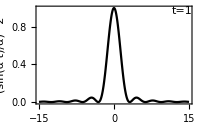

```mathematica
Plot[Sinc[α]^2,{α,-15,15},Epilog->{Text["\!\(t=1\)",Scaled@{1,1},{1.5,1.5}]},FrameLabel->{"\!\(α=(ω\_\(fi\)-ω)/2\)","\!\((sin(α t)/α)\^2\)"},PlotStyle->Black,PlotRange->All,ImageSize->200]
```

In the long-time limit of t→∞,

lim_(t→∞) 1/t((sin α t)/α)^2=π δ(α)=2π δ(2α).

This leads to the following expression for the transition rate,

W_(i→f)=lim_(t→∞) (P_(i→f)(t))/t=(2π)/ℏ(|fVi|)^2 δ(E_f-E_i-ℏ ω).

This is known as Fermi’s golden rule.

One might worry that in the t→∞ limit, the transition probability is in fact diverging. How can we justify the use of perturbation theory? For a transition with ω_fi≠ω, the “long time” limit is reached when t≫1/(ω_fi-ω), a value that can still be very short compared with the mean transition time, which is set by the matrix element ℏ/|fVi|.

Energy conservation is enforced in the long-time limit

E_f-E_i=ℏ ω,

such that transition occurs between levels in resonant with the the frequency of the perturbation.

#### Adiabatic Process

Consider the perturbation is gradually turn on following an exponential grow from the infinite past (and switch off after t=0)

V(t)=Piecewise[{{V e^(t/τ), t<0}, {0, t≥0}}].

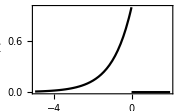

```mathematica
Plot[Exp[t]UnitStep[-t],{t,-5,2},PlotStyle->Black,PlotRange->All,FrameLabel->{"\!\(t\)","\!\(V(t)\)"},ImageSize->180]
```

Suppose the system is prepared in state i in the infinite past (t_0→-∞), what is the probability for the system to transit to the state f at t=0?

According to Eq. (DisplayFormulaNumbered),

P_(i→f)=1/ℏ^2(|∫_(-∞)^0 ⅆ t_1fVi e^(t_1/τ)e^(ⅈ ω_fi t_1)|)^2
=(|fVi|)^2/((E_f-E_i)^2+ℏ^2/τ^2).

The transition probability exhibits a resonance around ω_f=ω_i: states are more likely to hybridize when they are closer in energy.

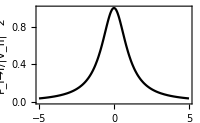

```mathematica
Plot[1/(ω^2+1),{ω,-5,5},PlotStyle->Black,FrameLabel->{"\!\((E\_f-E\_i)τ/ℏ\)","\!\(P\_\(i→f\)/|V\_\(fi\)|\^2\)"},ImageSize->200]
```

In the adiabatic limit of τ→∞, the perturbation is turned on very slowly, such that the H_0 eigenstate i simply evolves to the corresponding eigenstate of H=H_0+V, which is given by

i(V)=i+∑_(m≠i) m V_mi/(E_i-E_m)+…,

according to the time-independent perturbation, c.f. Eq. (DisplayFormulaNumbered). Then the probability to observe the system in the state f will be

(|fi(V)|)^2=(|V_fi|)^2/(E_i-E_f)^2,

which matches the result of time-dependent perturbation Eq. (DisplayFormulaNumbered) in the limit of τ→∞. Thus we have verified that the time-dependent perturbation falls back to the time-independent perturbation if the perturbation changes slow enough in time.

On the other hand, for any realistic physical process, the time scale τ can not be infinitely long. A finite τ sets an energy resolution ℏ τ^-1 (due to the uncertainty principle), below which the energy level resonance is smoothed out. So the singularity of the energy denominator in the time-independent perturbation do not actually occur in reality.